## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.2; Q=0.95;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.177364-7.96887×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.144789

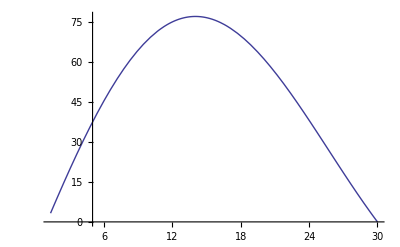

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-7.96901×10^-8},{30.2,-7.51995×10^-8},{30.4,-7.09633×10^-8},{30.6,-6.6979×10^-8},{30.8,-6.32219×10^-8},{31.,-5.96767×10^-8},{31.2,-5.63422×10^-8},{31.4,-5.3181×10^-8},{31.6,-5.02127×10^-8},{31.8,-4.73991×10^-8},{32.,-4.47546×10^-8},{32.2,-4.22501×10^-8},{32.4,-3.98835×10^-8},{32.6,-3.76379×10^-8},{32.8,-3.55332×10^-8},{33.,-3.35317×10^-8},{33.2,-3.16459×10^-8},{33.4,-2.9862×10^-8},{33.6,-2.81717×10^-8},{33.8,-2.65673×10^-8},{34.,-2.50539×10^-8},{34.2,-2.36204×10^-8},{34.4,-2.22667×10^-8},{34.6,-2.09862×10^-8},{34.8,-1.97682×10^-8},{35.,-1.86154×10^-8},{35.2,-1.75245×10^-8},{35.4,-1.64923×10^-8},{35.6,-1.55143×10^-8},{35.8,-1.45831×10^-8},{36.,-1.37057×10^-8},{36.2,-1.28711×10^-8},{36.4,-1.20824×10^-8},{36.6,-1.13332×10^-8},{36.8,-1.06226×10^-8},{37.,-9.95052×10^-9},{37.2,-9.31167×10^-9},{37.4,-8.70664×10^-9},{37.6,-8.13213×10^-9},{37.8,-7.58738×10^-9},{38.,-7.07228×10^-9},{38.2,-6.58236×10^-9},{38.4,-6.11818×10^-9},{38.6,-5.67833×10^-9},{38.8,-5.26005×10^-9},{39.,-4.86277×10^-9},{39.2,-4.48874×10^-9},{39.4,-4.1333×10^-9},{39.6,-3.79511×10^-9},{39.8,-3.47515×10^-9},{40.,-3.17175×10^-9},{40.2,-2.88409×10^-9},{40.4,-2.61141×10^-9},{40.6,-2.35301×10^-9},{40.8,-2.10819×10^-9},{41.,-1.87614×10^-9},{41.2,-1.65635×10^-9},{41.4,-1.44808×10^-9},{41.6,-1.25089×10^-9},{41.8,-1.06424×10^-9},{42.,-8.87544×10^-10},{42.2,-7.20365×10^-10},{42.4,-5.62218×10^-10},{42.6,-4.12548×10^-10},{42.8,-2.70425×10^-10},{43.,-1.37441×10^-10},{43.2,-1.11382×10^-11},{43.4,1.08152×10^-10},{43.6,2.20828×10^-10},{43.8,3.27076×10^-10},{44.,4.27186×10^-10},{44.2,5.21837×10^-10},{44.4,6.10848×10^-10},{44.6,6.94744×10^-10},{44.8,7.73596×10^-10},{45.,8.47903×10^-10},{45.2,9.17513×10^-10},{45.4,9.82931×10^-10},{45.6,1.04447×10^-9},{45.8,1.10201×10^-9},{46.,1.15585×10^-9},{46.2,1.20627×10^-9},{46.4,1.25313×10^-9},{46.6,1.29717×10^-9},{46.8,1.33802×10^-9},{47.,1.37597×10^-9},{47.2,1.42105×10^-9},{47.4,1.444×10^-9},{47.6,1.47424×10^-9},{47.8,1.50224×10^-9},{48.,1.52833×10^-9},{48.2,1.55167×10^-9},{48.4,1.57328×10^-9},{48.6,1.59288×10^-9},{48.8,1.6108×10^-9},{49.,1.62697×10^-9},{49.2,1.64138×10^-9},{49.4,1.65437×10^-9},{49.6,1.66588×10^-9},{49.8,1.6759×10^-9},{50.,1.68456×10^-9},{50.2,1.69189×10^-9},{50.4,1.69824×10^-9},{50.6,1.70349×10^-9},{50.8,1.70754×10^-9},{51.,1.71056×10^-9},{51.2,1.71263×10^-9},{51.4,1.71378×10^-9},{51.6,1.71852×10^-9},{51.8,1.71353×10^-9},{52.,1.72818×10^-9},{52.2,1.71015×10^-9},{52.4,1.70739×10^-9},{52.6,1.704×10^-9},{52.8,1.69979×10^-9},{53.,1.68939×10^-9},{53.2,1.68991×10^-9},{53.4,1.68466×10^-9},{53.6,1.67839×10^-9},{53.8,1.67177×10^-9},{54.,1.6637×10^-9},{54.2,1.65723×10^-9},{54.4,1.64948×10^-9},{54.6,1.64098×10^-9},{54.8,1.63276×10^-9},{55.,1.62389×10^-9},{55.2,1.61468×10^-9},{55.4,1.60537×10^-9},{55.6,1.59565×10^-9},{55.8,1.58577×10^-9},{56.,1.57574×10^-9},{56.2,1.56548×10^-9},{56.4,1.55496×10^-9},{56.6,1.54429×10^-9},{56.8,1.53333×10^-9},{57.,1.52253×10^-9},{57.2,1.51132×10^-9},{57.4,1.50026×10^-9},{57.6,1.48894×10^-9},{57.8,1.47732×10^-9},{58.,1.46605×10^-9},{58.2,1.45452×10^-9},{58.4,1.44289×10^-9},{58.6,1.43103×10^-9},{58.8,1.41945×10^-9},{59.,1.40759×10^-9},{59.2,1.39585×10^-9},{59.4,1.38405×10^-9},{59.6,1.37213×10^-9},{59.8,1.36032×10^-9},{60.,1.34849×10^-9}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

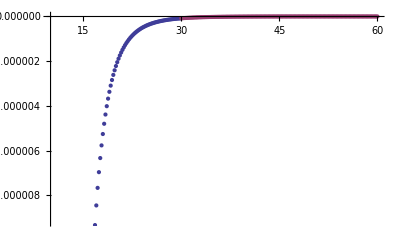

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

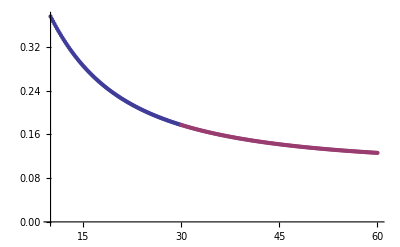

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.2/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.2/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.2/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.2/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```